```mathematica
(*Import the data*)
```

```mathematica
data=Import["./Downloads/transposed_data_subset_species_level.tsv","tsv"];
```

```mathematica
Transpose[data][[2]]
```

{k__Bacteria|p__Acidobacteria|c__Acidobacteriia|o__Acidobacteriales|f__Acidobacteriaceae|g__Granulicella|s__Granulicella_unclassified,0.,0.,0.,0.,0.,0.,0.,0.,0.0000504,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(*for h4023*)
```

```mathematica
h4023={};
Do[AppendTo[h4023,Drop[Transpose[data][[n]],-22]],{n,1,Length[Transpose[data]]}]
```

```mathematica
(*Transpose data to select the top 15 species*)
```

```mathematica
h4023[[2]]
```

{k__Bacteria|p__Acidobacteria|c__Acidobacteriia|o__Acidobacteriales|f__Acidobacteriaceae|g__Granulicella|s__Granulicella_unclassified,0.,0.,0.,0.,0.,0.,0.,0.,0.0000504,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
trans=h4023;
total={};
Do[AppendTo[total,Total[Drop[trans[[n]],1]]],{n,2,Length[trans]}]
```

```mathematica
topx=15;
```

```mathematica
top15={};
Do[AppendTo[top15,trans[[Flatten[Position[total,TakeLargest[total,topx][[n]]]]+1]]],{n,1,topx}]
```

```mathematica
(*put all the information for plotting in one*)
```

```mathematica
Length[top15[[1,1]]]
```

23

```mathematica
Length[top15]
```

15

```mathematica
top15[[1]]
```

{{k__Bacteria|p__Bacteroidetes|c__Bacteroidia|o__Bacteroidales|f__Prevotellaceae|g__Prevotella|s__Prevotella_copri,0.,0.,0.,0.742188,0.472312,0.46144,0.0865114,0.0676526,0.0004213,0.692461,0.455287,0.196086,0.133742,0.550559,0.114389,0.142428,0.0475071,0.624035,0.281901,0.0026321,0.0070066,0.202475}}

```mathematica
Transpose[data][[1]]
```

{,HSM67VDR_P,HSM6XRUL,HSM6XRUN,HSM6XRUR,HSM6XRQ8,HSM7CZ16,HSM7CZ18,HSM7CZ1A,HSM7CZ1C,HSM7CZ1E,HSM7CZ1G,HSM7J4HA,HSM7J4HC,HSM7J4HE,HSM7J4HG,HSM7J4HI,HSM7J4HK,HSM7J4KC,HSM7J4KG,HSM7J4KI,HSM7J4KK,HSM7J4KM,HSM5MD5X_P,HSM5MD62,HSM5MD6Y,HSM5MD71,HSM5MD73,HSM5MD75,HSM6XRS4,HSM6XRS6,HSM6XRS8,HSM6XRSE,HSM7CYZ5,HSM7CYZ7,HSM7CYZ9,HSM7CYZB,HSM7CYZD,HSM7CYZF,HSM7J4QB,HSM7J4QD,HSM7J4QF,HSM7J4QH,HSM7J4QJ,HSM7J4QL}

```mathematica
all={};
AppendTo[all,Drop[Transpose[data][[1]],-22]];Do[AppendTo[all,Flatten[top15[[n]]]],{n,1,topx}]
```

```mathematica
Length[top15]
```

15

```mathematica
(*add "other" for all the samples*)
```

```mathematica
Length[all]
```

16

```mathematica
Length[all[[3]]]
```

23

```mathematica
other={};
Do[AppendTo[other,1-Total[Drop[Transpose[all][[n]],1]]],{n,2,23}]
```

```mathematica
all = Insert[all,Flatten[{"other",other}],2];
```

```mathematica
Length[all]
```

17

```mathematica
(*create the genus name for labeling*)
names={};
Do[AppendTo[names,StringSplit[Transpose[all][[1]],"|"][[n,7]]],{n,3,Length[Transpose[all][[1]]]}]
```

```mathematica
names
```

{s__Prevotella_copri,s__Bacteroides_sp_4_3_47FAA,s__Faecalibacterium_prausnitzii,s__Bacteroides_massiliensis,s__Bacteroides_vulgatus,s__Alistipes_putredinis,s__Eubacterium_rectale,s__Bacteroides_caccae,s__Phascolarctobacterium_succinatutens,s__Parabacteroides_merdae,s__Paraprevotella_unclassified,s__Bacteroides_stercoris,s__Subdoligranulum_unclassified,s__Akkermansia_muciniphila,s__Barnesiella_intestinihominis}

```mathematica
namesn={};
Do[AppendTo[namesn,Capitalize[StringSplit[names,"__"][[n,2]]]],{n,1,Length[names]}]
```

```mathematica
namesn
```

{Prevotella_copri,Bacteroides_sp_4_3_47FAA,Faecalibacterium_prausnitzii,Bacteroides_massiliensis,Bacteroides_vulgatus,Alistipes_putredinis,Eubacterium_rectale,Bacteroides_caccae,Phascolarctobacterium_succinatutens,Parabacteroides_merdae,Paraprevotella_unclassified,Bacteroides_stercoris,Subdoligranulum_unclassified,Akkermansia_muciniphila,Barnesiella_intestinihominis}

```mathematica
namesn1=Insert[namesn,"other",1]
```

{other,Prevotella_copri,Bacteroides_sp_4_3_47FAA,Faecalibacterium_prausnitzii,Bacteroides_massiliensis,Bacteroides_vulgatus,Alistipes_putredinis,Eubacterium_rectale,Bacteroides_caccae,Phascolarctobacterium_succinatutens,Parabacteroides_merdae,Paraprevotella_unclassified,Bacteroides_stercoris,Subdoligranulum_unclassified,Akkermansia_muciniphila,Barnesiella_intestinihominis}

```mathematica
Length[namesn1]
```

16

```mathematica
(*Plotting*)
```

```mathematica
data=Drop[Transpose[Drop[all,1]],1];
```

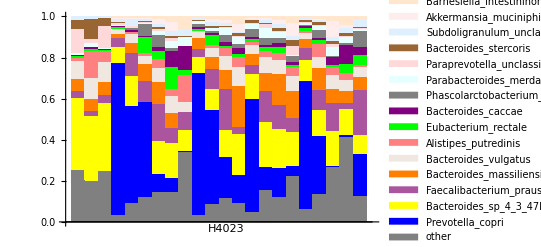

```mathematica
BarChart[data,ChartLabels->{{,,,,,,,,,,,"H4023",,,,,,,,,},None},
ChartLayout -> "Stacked",ChartStyle -> { Gray,Blue,Yellow,Blend[{Purple,LightYellow},1/3],Orange, LightBrown,Pink,Green, Purple, Gray,LightCyan,LightRed,Brown, LightBlue, LightPink,LightOrange},ChartLegends->namesn1,BaseStyle->{FontWeight->"Bold",FontSize->12},AxesStyle->Directive[Black,12]]
```